B

(Cos[q1[t]] Cos[q2[t]] Cos[q3[t]]-Sin[q1[t]] Sin[q3[t]] | -Cos[q3[t]] Sin[q2[t]] | Cos[q2[t]] Cos[q3[t]] Sin[q1[t]]+Cos[q1[t]] Sin[q3[t]]
Cos[q1[t]] Sin[q2[t]] | Cos[q2[t]] | Sin[q1[t]] Sin[q2[t]]
-Cos[q3[t]] Sin[q1[t]]-Cos[q1[t]] Cos[q2[t]] Sin[q3[t]] | Sin[q2[t]] Sin[q3[t]] | Cos[q1[t]] Cos[q3[t]]-Cos[q2[t]] Sin[q1[t]] Sin[q3[t]])

IB

(Ibb+l^2 m | 0 | 0
0 | Ibb | 0
0 | 0 | Ibb+l^2 m)

A

(0 | -Cos[q1[t]] q2'[t]-Sin[q1[t]] Sin[q2[t]] q3'[t] | q1'[t]+Cos[q2[t]] q3'[t]
Cos[q1[t]] q2'[t]+Sin[q1[t]] Sin[q2[t]] q3'[t] | 0 | Sin[q1[t]] q2'[t]-Cos[q1[t]] Sin[q2[t]] q3'[t]
-q1'[t]-Cos[q2[t]] q3'[t] | -Sin[q1[t]] q2'[t]+Cos[q1[t]] Sin[q2[t]] q3'[t] | 0)

W

(-Sin[q1[t]] q2'[t]+Cos[q1[t]] Sin[q2[t]] q3'[t]
q1'[t]+Cos[q2[t]] q3'[t]
Cos[q1[t]] q2'[t]+Sin[q1[t]] Sin[q2[t]] q3'[t])

L

-g l m Cos[q2[t]]+1/2 (Ibb (q1'[t]+Cos[q2[t]] q3'[t])^2+(Ibb+l^2 m) (-Sin[q1[t]] q2'[t]+Cos[q1[t]] Sin[q2[t]] q3'[t])^2+(Ibb+l^2 m) (Cos[q1[t]] q2'[t]+Sin[q1[t]] Sin[q2[t]] q3'[t])^2)

Ibb (-Sin[q2[t]] q2'[t] q3'[t]+q1''[t]+Cos[q2[t]] q3''[t])

-g l m Sin[q2[t]]+Ibb Sin[q2[t]] q1'[t] q3'[t]-l^2 m Cos[q2[t]] Sin[q2[t]] q3'[t]^2+Ibb q2''[t]+l^2 m q2''[t]

-Ibb Sin[q2[t]] q1'[t] q2'[t]+l^2 m Sin[2 q2[t]] q2'[t] q3'[t]+Ibb Cos[q2[t]] q1''[t]+Ibb q3''[t]+1/2 l^2 m q3''[t]-1/2 l^2 m Cos[2 q2[t]] q3''[t]

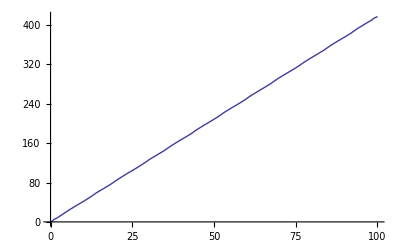

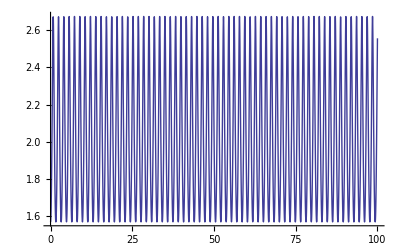

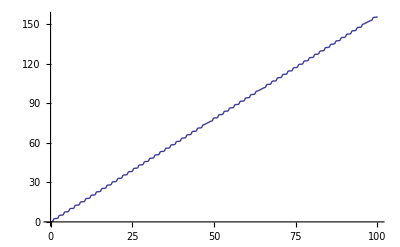

-Graphics3D-

-Graphics3D-

```mathematica
Clear["Global`*"];
(* Q - parameters Q = (q1 == alpha) *)
(* Configuration *)


B = Simplify[RotationMatrix[q3[t], {0,1,0}].RotationMatrix[q2[t], {0,0,1}].RotationMatrix[q1[t], {0,1,0}]];


IB = DiagonalMatrix[{Ibb + m*l^2, Ibb, Ibb + m*l^2}];
(* Antisymmetric matrix, To get angular velocity *)
A =Simplify[ Transpose[B].D[B,t]];
W= {
A[[3,2]], 
A[[1,3]], 
A[[2,1]]};

(* Kinetic - Potential *)
(* Potential energy in Scene *)
L = W.IB.W/2 - m*g*(Simplify[B.{0,l,0}])[[2]];

Print["B"]
MatrixForm[B]
Print["IB"]
MatrixForm[IB]
Print["A"]
MatrixForm[A]
Print["W"]
MatrixForm[W]
Print["L"]
L

dtdq1 = D[D[L,q1'[t]],t];
dq1 = D[L,q1[t]];
LangrageDiff1 = Simplify[dtdq1 - dq1];

dtdq2 = D[D[L,q2'[t]],t];
dq2 = D[L,q2[t]];
LangrageDiff2 = Simplify[dtdq2 - dq2];

dtdq3 = D[D[L,q3'[t]],t];
dq3 = D[L,q3[t]];
LangrageDiff3 = Simplify[dtdq3 - dq3];

LangrageDiff1
LangrageDiff2
LangrageDiff3

(* Example *)
r1 = LangrageDiff1;
r2 = LangrageDiff2;
r3 = LangrageDiff3;

Ibb=1;
l=1;
m=1;
g=9.81;
T=100;

sol=NDSolve[{
r1==0,r2==0,r3==0,
q1[0]==0,q1'[0]==3,
q2[0]==Pi/2,q2'[0]==0,
q3[0]==0,q3'[0]==0},
{q1,q2,q3},{t,0,T}];
q1=First[q1/.sol];
q2=First[q2/.sol];
q3=First[q3/.sol];

Plot[q1[t],{t,0,T}]
Plot[q2[t],{t,0,T}]
Plot[q3[t],{t,0,T}]
ParametricPlot3D[{q1[t],q2[t],q3[t]},{t,0,T}]
ParametricPlot3D[B.{0,l,0},{t,0,T},PlotStyle->Thick,PlotRange->{{-1,1},{-1,1},{-1,1}}]
Animate[Graphics3D[{Line[{{-1.5,0,0},{1.5,0,0}}],Line[{{0,-1.5,0},{0,1.5,0}}],Line[{{0,0,-1.5},{0,0,1.5}}],Arrow[{{0,0,0},{-Cos[q3[t]] Sin[q2[t]],Cos[q2[t]],Sin[q2[t]] Sin[q3[t]]}}]}],{t,0,T}]
```